# Beam Fitting Last Updated: 03/31/2022

```mathematica
Quit[];
```

```mathematica
(*Remove["Global`*"];ClearInOut[];*)
```

## Prep

## Plotting Setup

```mathematica
SetOptions[Plot,ImageSize->Large,PlotRange->Full];
SetOptions[ListPlot,ImageSize->Large,PlotRange->Full];
```

```mathematica
Off[General::munfl];
```

## Global Variables

```mathematica
inch=2.54*^-2;
cm=1*^-2;mm=1*^-3;um=1*^-6;nm=1*^-9;
```

```mathematica
pixelWidth=4.4*^-6;(*length per pixel for pixelink camera*)
```

## Image Import

```mathematica
(*set directory and filetype*)
(*SetDirectory["/Users/claytonho/Documents/Research/Mathematica/Beams/Data/849_waist"]*)
SetDirectory["D:\\729_Injection_Lock_Beam_Shaping"];

(*ParallelEvaluate[SetDirectory["/Users/claytonho/Documents/Research/Mathematica/Beams/Data/849_waist"]];*)
ParallelEvaluate[SetDirectory["D:\\729_Injection_Lock_Beam_Shaping"]];
imgNames=FileNames["*bmp*"]
```

{729_beam_shaping_1in.bmp,729_beam_shaping_2in.bmp,729_beam_shaping_3in.bmp,729_beam_shaping_4in.bmp,729_beam_shaping_5in.bmp}

```mathematica
λ0=729*nm;(*wavelength*)
waistDist={12,15,18,21,24,27,30,3,6,9}*inch;(*beam waist measurement distances*)
waistDist = {1,2,3,4,5}*inch
```

{0.0254,0.0508,0.0762,0.1016,0.127}

## Process Images

## Get Images

```mathematica
AbsoluteTiming[
imdRaw=ParallelMap[Import,imgNames];
imdRaw=ColorConvert[#,"Grayscale"]&/@imdRaw;(*for bmp only*)
imdRaw=ImageData/@imdRaw;
]
```

{1.09502,Null}

```mathematica
(*number of images*)
numImages=Length[imgNames];
(*image dimensions*)
imgDim=Dimensions[imdRaw[[1]]]//Reverse;
```

```mathematica
(*order images by measurement distance*)
distOrder=Ordering[waistDist];
waistDist=Sort[waistDist];
imdRaw=imdRaw[[distOrder]];
```

## Check Saturation/Clipping

{5,1200}

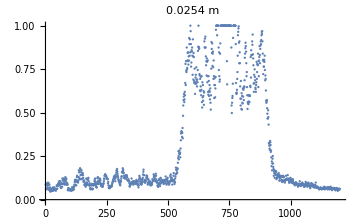
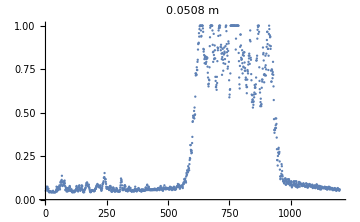
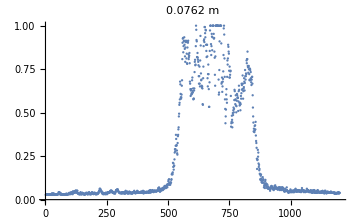
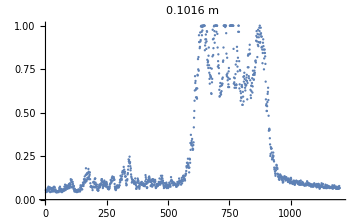
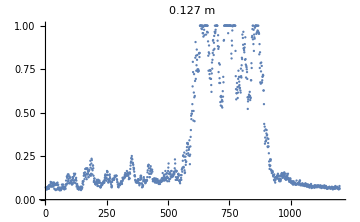

```mathematica
imdMax=Map[Max,imdRaw,{2}];imdMax//Dimensions
Table[ListPlot[imdMax[[i]],ImageSize->Medium,PlotRange->{0,1},PlotLabel->ToString[waistDist[[i]]]<>" m"],{i,1,numImages}]
```

```mathematica
nGauss=30;(*gaussian kernel, i.e. 2σ*)
window={500,500};(*range of pixels to take in*)
```

## Gaussian Fit from Center

```mathematica
AbsoluteTiming[
imdGauss=ParallelMap[GaussianFilter[#,nGauss]&,imdRaw];
center=ParallelMap[Reverse[Position[#,Max[#]][[1]]]&,imdGauss];
]
```

{1.54384,Null}

```mathematica
{x1,x2}=Transpose[Clip[{#-window[[1]],#+window[[1]]},{1,imgDim[[1]]}]&/@center[[;;,1]]];
{y1,y2}=Transpose[Clip[{#-window[[2]],#+window[[2]]},{1,imgDim[[2]]}]&/@center[[;;,2]]];
```

```mathematica
imdProcessed=Table[imdRaw[[i,y1[[i]];;y2[[i]],x1[[i]];;x2[[i]]]],{i,numImages}];
```

## Compare With/Without Gaussian Filter

```mathematica
AbsoluteTiming[imdProcessedGauss=ParallelMap[GaussianFilter[#,nGauss]&,imdProcessed];]
```

{0.33362,Null}

```mathematica
(*Image[#/Max[#]]&/@imdProcessed
Image[#/Max[#]]&/@imdProcessedGauss*)
```

## Fit Images

## Fit Setup

```mathematica
(*sum along axes*)
trans=Transpose[#]&/@imdProcessed;
xList=Total[#]&/@imdProcessed;
yList=Total[#]&/@trans;
```

```mathematica
th1=Table[{imdGauss[[i,center[[i,2]],;;]],imdGauss[[i,;;,center[[i,1]]]]},{i,1,Length[imdGauss]}];
xList=th1[[;;,1]];yList=th1[[;;,2]];
```

```mathematica
(*fitting constraints*)
(*note - adding constraints may hurt fitting*)
xFitConstr={};
yFitConstr={};
```

```mathematica
(*factor of 2 in exponent is b/c intensity is square of electric field*)
xFitEqn={a(Exp[-2((x-x0)/wx)^2])+b};
yFitEqn={a(Exp[-2((y-y0)/wy)^2])+b};
```

## Fitting

```mathematica
(*fitting parameters*)
(*xFitVars=Table[{{x0,Min[{center[[i,1]],500}]},{wx,300},{a,Max[xList[[i]]]},{b,Min[xList[[i]]]}},{i,1,numImages}];
yFitVars=Table[{{y0,Min[{500,center[[i,2]]}]},{wy,150},{a,Max[yList[[i]]]},{b,Min[yList[[i]]]}},{i,1,numImages}];*)
xFitVars=Table[{{x0,center[[i,1]]},{wx,300},{a,Max[xList[[i]]]},{b,Min[xList[[i]]]}},{i,1,numImages}];
yFitVars=Table[{{y0,center[[i,2]]},{wy,150},{a,Max[yList[[i]]]},{b,Min[yList[[i]]]}},{i,1,numImages}];
```

```mathematica
(*fit!*)
AbsoluteTiming[
xFit=ParallelTable[NonlinearModelFit[xList[[i]],Join[xFitEqn,xFitConstr],xFitVars[[i]],x,MaxIterations->1*^6],{i,1,numImages}];
yFit=ParallelTable[NonlinearModelFit[yList[[i]],Join[yFitEqn,yFitConstr],yFitVars[[i]],y,MaxIterations->1*^6],{i,1,numImages}];
]
```

{0.0524059,Null}

```mathematica
xFitParams=#["ParameterTable"]&/@xFit
yFitParams=#["ParameterTable"]&/@yFit
```

{ | Estimate | Standard Error | t-Statistic | P-Value
x0 | 894.597 | 1.44007 | 621.217 | 0.
wx | 237.734 | 3.17817 | 74.8021 | 0.
a | 0.316788 | 0.00344216 | 92.0316 | 0.
b | 0.00832387 | 0.0012661 | 6.57439 | 6.59882×10^-11, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 721.08 | 0.783502 | 920.33 | 0.
wx | 166.768 | 1.66411 | 100.215 | 0.
a | 0.47532 | 0.0039494 | 120.352 | 0.
b | 0.010352 | 0.00112892 | 9.16988 | 1.41648×10^-19, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 775.869 | 0.888685 | 873.052 | 0.
wx | 169.087 | 1.88958 | 89.4836 | 0.
a | 0.42741 | 0.00397441 | 107.54 | 0.
b | 0.00929524 | 0.00114654 | 8.10718 | 1.02131×10^-15, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 869.095 | 0.85887 | 1011.91 | 0.
wx | 168.392 | 1.82559 | 92.2402 | 0.
a | 0.489742 | 0.00441886 | 110.83 | 0.
b | 0.00909998 | 0.00127127 | 7.15818 | 1.24223×10^-12, | Estimate | Standard Error | t-Statistic | P-Value
x0 | 872.36 | 1.29905 | 671.537 | 0.
wx | 207.916 | 2.81741 | 73.7967 | 0.
a | 0.396641 | 0.00441645 | 89.81 | 0.
b | 0.00911228 | 0.00147011 | 6.19839 | 7.2469×10^-10}

{ | Estimate | Standard Error | t-Statistic | P-Value
y0 | 736.862 | 1.48659 | 495.672 | 0.
wy | 251.959 | 3.53928 | 71.1892 | 0.
a | 0.361941 | 0.00395075 | 91.6133 | 0.
b | 0.039476 | 0.001957 | 20.1717 | 4.06715×10^-78, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 737.978 | 3.13674 | 235.269 | 0.
wy | 288.908 | 7.84671 | 36.819 | 5.07398×10^-199
a | 0.287284 | 0.00591627 | 48.5582 | 4.10585×10^-285
b | 0.0216489 | 0.00336309 | 6.43721 | 1.75763×10^-10, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 675.967 | 2.97025 | 227.579 | 0.
wy | 279.673 | 7.36807 | 37.9574 | 1.50038×10^-207
a | 0.271966 | 0.00543762 | 50.0156 | 2.07855×10^-295
b | 0.0125872 | 0.00300532 | 4.18829 | 0.0000301702, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 732.139 | 2.61365 | 280.121 | 0.
wy | 255.465 | 6.25135 | 40.8656 | 3.25085×10^-229
a | 0.313555 | 0.0059466 | 52.7285 | 2.72631×10^-314
b | 0.0278017 | 0.0029862 | 9.31006 | 5.91963×10^-20, | Estimate | Standard Error | t-Statistic | P-Value
y0 | 752.581 | 1.08878 | 691.213 | 0.
wy | 211.51 | 2.4767 | 85.3996 | 0.
a | 0.434663 | 0.00406101 | 107.033 | 0.
b | 0.0447124 | 0.00171538 | 26.0655 | 5.67806×10^-119}

```mathematica
{x0Fit,wxFit,axFit,bxFit}=Transpose[#[[1,1,2;; ,2]]&/@xFitParams];
{y0Fit,wyFit,ayFit,byFit}=Transpose[#[[1,1,2;; ,2]]&/@yFitParams];
```

## Show

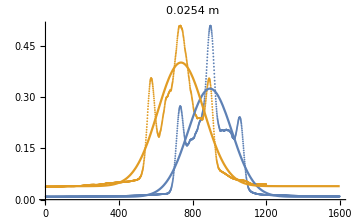
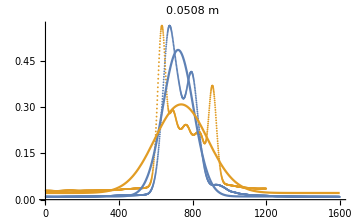
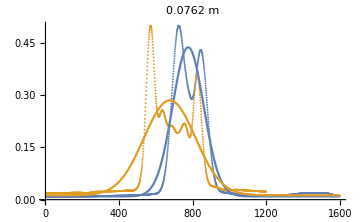
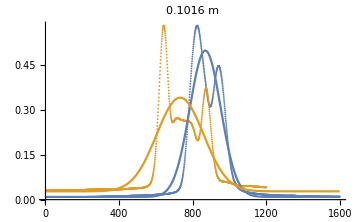
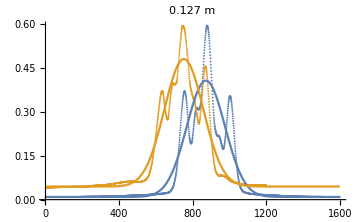

```mathematica
Table[Show[
ListPlot[{xList[[i]],yList[[i]]},ImageSize->Medium,PlotLabel->ToString[waistDist[[i]]]<>" m"],
(*Plot[{xFit[[i]][x],yFit[[i]][x]},{x,0,2 *window[[1]]+1}]*)
Plot[{xFit[[i]][x],yFit[[i]][x]},{x,0,1600}]
],{i,1,numImages}]
```

## Outputs

## Get Points

```mathematica
pos=Table[{x1[[i]]+x0Fit[[i]],y1[[i]]+y0Fit[[i]]},{i,numImages}];
pos=(#/.{x_,y_}->{x,imgDim[[2]]-y})&/@pos;
```

```mathematica
wxFitm=pixelWidth*wxFit;waistX=Transpose[{waistDist,Abs[wxFitm]}];
wyFitm=pixelWidth*wyFit;waistY=Transpose[{waistDist,Abs[wyFitm]}];
```

### Print Results

```mathematica
"w_x="<>ToString[#]<>"μm"&/@(10^6 wxFitm)
"w_y="<>ToString[#]<>"μm"&/@(10^6 wyFitm)
```

{w_x=1046.03μm,w_x=733.781μm,w_x=743.981μm,w_x=740.926μm,w_x=914.829μm}

{w_y=1108.62μm,w_y=1271.2μm,w_y=1230.56μm,w_y=1124.05μm,w_y=930.642μm}

## Get Errors

```mathematica
wxFitErr=#[[1,1,2;;,3]]&/@xFitParams;wxFitErr=wxFitErr[[;;,2]]*pixelWidth;
wyFitErr=#[[1,1,2;;,3]]&/@yFitParams;wyFitErr=wyFitErr[[;;,2]]*pixelWidth;
```

```mathematica
waistXError=Transpose[{waistDist,Abs[wxFitm[[#]]]±wxFitErr[[#]]&/@Range[numImages]}];
waistYError=Transpose[{waistDist,Abs[wyFitm[[#]]]±wyFitErr[[#]]&/@Range[numImages]}];
```

```mathematica
waistXError
waistYError
```

{{0.0254,0.00104603±0.000013984},{0.0508,0.000733781±7.3221×10^-6},{0.0762,0.000743981±8.31416×10^-6},{0.1016,0.000740926±8.03258×10^-6},{0.127,0.000914829±0.0000123966}}

{{0.0254,0.00110862±0.0000155728},{0.0508,0.0012712±0.0000345255},{0.0762,0.00123056±0.0000324195},{0.1016,0.00112405±0.0000275059},{0.127,0.000930642±0.0000108975}}

## Plot w/Error Bars

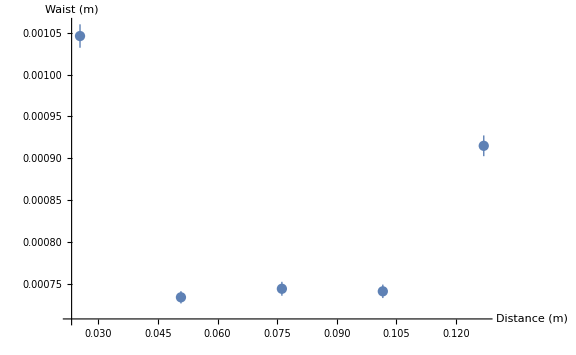
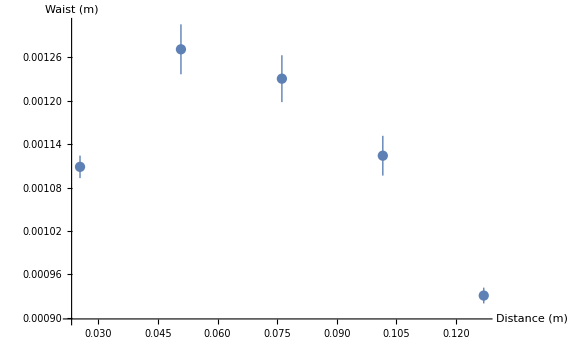

```mathematica
ListPlot[#,ImageSize->Large,PlotRange->Full,AxesLabel->{"Distance (m)","Waist (m)"}]&/@{waistXError,waistYError}
```

## Fit Beam Waist

## Setup

```mathematica
(*note - adding constraints may hurt fitting*)
waistXFitConstr={};
waistYFitConstr={};
```

```mathematica
waistXFitEqn=w0*√(1+((x-x0)/((π*w0^2)/λ0))^2);
waistYFitEqn=w0*√(1+((y-y0)/((π*w0^2)/λ0))^2);
```

```mathematica
waistXFitVars={{w0,Min[waistX[[;;,2]]]},{x0,0}};
waistYFitVars={{w0,Min[waistY[[;;,2]]]},{y0,0}};
```

## Fit

```mathematica
AbsoluteTiming[
waistXFit=NonlinearModelFit[waistX,Join[{waistXFitEqn},waistXFitConstr],waistXFitVars,x,MaxIterations->1*^5,ConfidenceLevel->0.99];
waistYFit=NonlinearModelFit[waistY,Join[{waistYFitEqn},waistYFitConstr],waistYFitVars,y,ConfidenceLevel->0.99];
]
```

{0.002723,Null}

```mathematica
{waistXFitParams,waistYFitParams}={waistXFit["ParameterTable"],waistYFit["ParameterTable"]};
{w0xFit,z0xFit}=Transpose[waistXFitParams[[1,1,2;; ,2]]];
{w0yFit,z0yFit}=Transpose[waistYFitParams[[1,1,2;; ,2]]];
```

## Show

```mathematica
{waistXFitParams,waistYFitParams}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
w0 | 0.000222542 | 0.000396031 | 0.561931 | 0.613411
x0 | 0.848855 | 1.27218 | 0.667245 | 0.552352, | Estimate | Standard Error | t-Statistic | P-Value
w0 | 0.000116529 | 0.0000887054 | 1.31366 | 0.28039
y0 | 0.642144 | 0.427123 | 1.50342 | 0.229765}

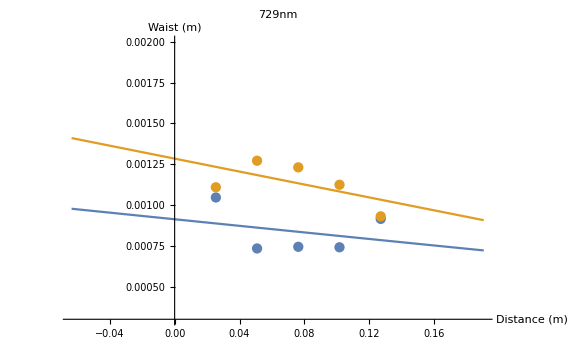

```mathematica
Show[
Plot[{waistXFit[x],waistYFit[x]},{x,-0.5*Max[waistDist],1.5*Max[waistDist]},PlotLabel->ToString[λ0/nm]<>"nm",AxesLabel->{"Distance (m)","Waist (m)"},PlotRange->{0.3mm,2mm}],
ListPlot[{waistX,waistY},PlotRange->Full]
]
```